# Heat across Si{P} sample

## How to run the program: -Set laser power (“Q”), “period”, and “maxTemp” in cell below. -To calculate temp evolution at a specific duty cycle, enter “duty” as a percentage, uncomment “sol”, comment out code under “Calculating temp evolutions for a series of D values”, and run cell below. Ensure “len” is at least 10^-3 (approximate time to reach steady state oscillations). “MaxStepFraction” under the NDSolve function works best when set to ~1/(50*len/period), but a larger fraction may be neccesary to avoid lengthy runtimes. -Then run the “Plotting” cell to view a plot of the temperature evolution (i.e. plots “sol”). -To maximize the duty cycle value for a specific laser power and period under the constraint of some maximum temperature, comment out “sol” and uncomment code under “Calculating temp evolutions for a series of D values”. -Create a range of D values with “dStart”, “dEnd”, and “dutyCycles” (# of elements in the inclusive range dStart to dEnd). Run the cell below followed by the cell “Maximizing Duty Cycle”. The second cell will calculate the maximum temperature (Tmax) attained for each D value in the set, and find the D value with the highest Tmax that does not exceed maxTemp, printing it along with the corresponding Tmax, as well as a plot of Tmax as a function of D. -NOTE: finding the maxValue of the interpolating function proves lengthy, so I found it best to use sol to find a small range of D values (~5) around the unknown Dmax value before running the “Maximizing Duty Cycle” cell. For the shortest periods, even running a few D values was taking a while, so I used sol with brute force to find Dmax, and then changed the range of “t” in “Plotting” from {t,0,len} to {t,len-period,len} to only view the final oscillation, where Tmax could be extrapolated visually.

### Parameters & heat eqn solver

```mathematica
(*delay=0.01;*)(*wait to turn on laser*)
Q=0.1;(*laser power in mW*)
kappa=vSound*mfp/3.;
vSound=5.07*10^6;(*mm s^-1*)
mMolar=0.028;(*kg mol^-1*)
mfp=0.08;(*mm*)
nAv=6.022*10^23;
kB=1.38*10^-23;
tD=647;(*Debye temp*)
c[T_]:= (12/5)*Pi^4*nAv*kB*(T/tD)^3;
rho=2.34*10^-6;(*kg mm^-3*)
length=8;(*mm*)
width=2.22;(*mm*)
height=2.12;(*mm*)
volume=length*width*height;
cpInv=mMolar/(c[f[x,t]]*rho*volume);
squareWave[t_,period_,duty_]:=HeavisideTheta[1-Mod[t/period,1.]/duty];

Duty Cycle Parameters;
period=1*10^-3;
duty=50;
maxTemp=2.17;

len=1*period;(*0.7*10^-3;*)

T[duty_]:=NDSolve[{D[f[x,t],t]-kappa*D[f[x,t],x,x]==squareWave[t,period,duty/100]*cpInv*(Q/1000)(**Exp[-x/44.8]*),f[x,0]==0.3,f[0,t]==0.3,(D[f[x,t],x]/.x->length)==0},f,{x,0,length},{t,0,len},MaxStepFraction->1/1000];

count=0;

While[count<1,sol=T[duty](*single temp evolution calculated w/ duty*); Print[MaxValue[{f[8,t]/.sol[[1]][[1]],(len-period)<t<len},t]]; Q=Q+0.5; count++]

Calculating temp evolutions for a series of D values;
(*dutyCycles=3;
dStart=1;
dEnd=3;

maxTemps=ConstantArray[0,{dutyCycles,2}];
duties=Range[dStart,dEnd,(dEnd-dStart)/(dutyCycles-1)];
result=Array[T,dutyCycles,{dStart,dEnd}];*)
```

1.22181

### Maximizing Duty Cycle (plots T[D]; prints Dmax and T[Dmax]; run above cell first)

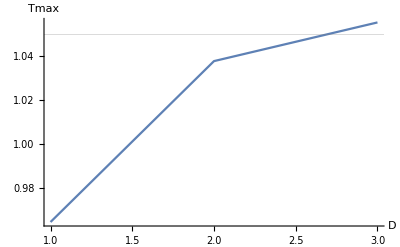

2

1.03786

```mathematica
loop=dutyCycles;While[loop>0,maxTemps[[loop]][[2]]=MaxValue[{f[6,t]/.result[[loop]][[1]],(len-period)<t<len},t];maxTemps[[loop]][[1]]=duties[[loop]];loop--];
ListLinePlot[maxTemps,AxesLabel->{D,Tmax},GridLines->{{},{maxTemp}}]
loop=dutyCycles;
While[loop>0,If[maxTemps[[loop]][[2]]>maxTemp,loop--,Print[maxTemps[[loop]][[1]]];Print[maxTemps[[loop]][[2]]];Break[]]]
```

### Plotting (if sol is uncommented)

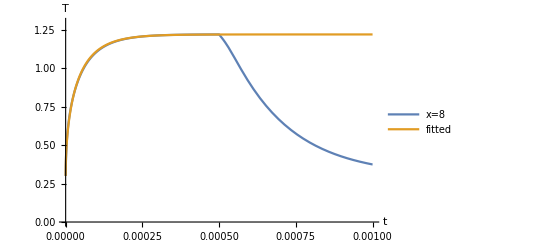

```mathematica
(*Plot3D[f[x,t]/.sol,{x,0,8},{t,0,10*period},AxesLabel->{x,t,T}]*)
tt=f[8,0.0005]/.sol[[1]];
tM =tt-0.3;
Plot[{f[8,t]/.sol(*,squareWave[t,period,duty/100]*), tM*Erf[InverseErf[(tM-0.0001)/tM]*Sqrt[t]/Sqrt[6.2*10^-4]]+0.3},{t,0,0.001},PlotRange->{0,1.3},AxesLabel->{"t", "T"},PlotLegends->{"x=8", "fitted"},GridLines->{{},{maxTemp}}]
(*MaxValue[{f[8,t]/.sol[[1]],(len-period)<t<len},t]*)
```

```mathematica
f[6,0.0005]/.sol[[1]]
```

1.18541

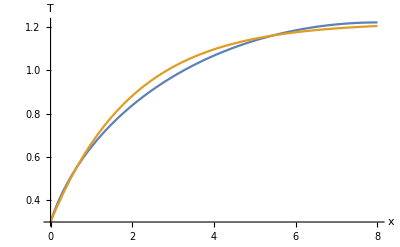

```mathematica
Tend = 1.2222460237829527;
Plot[{f[x,0.0005]/.sol,(Tend-0.3)*(1-Exp[-x/2])+0.3}, {x,0,8}, AxesLabel->{"x","T"}(*, PlotRange->{0.3,Tend+0.1}*)]
```

```mathematica
Sqrt[8]/InverseErf[0.999953]
```

0.982785

```mathematica
1/%
```

1.01752

```mathematica
With[{n=1,L=length,a0=0.06755564087081681,a1=19.720561339738595,a2=76.81985966506535,a3=-4.8012412290665845},2*NIntegrate[x*Sin[(n-1/2)*Pi*x/L]*(0.3-a0*Sqrt[a1+a2*x+a2*x^2]), {x,0, L}]/L]
```

-22.3

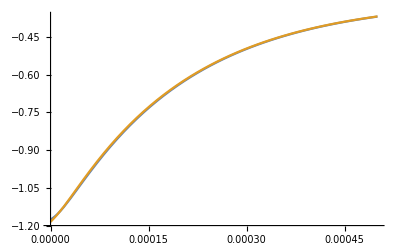

```mathematica
length=8;
Tstop=1.2218-0.3;
fs[x_,n_,L_,t_,Tstop_]:=Tstop*(4*L/Pi)*(L+(-1)^(n+1)*(2n-1)*Pi*Exp[-L/2])/((2n-1)*(L^2+((2n-1)*Pi)^2))*Sin[(2n-1)*Pi*x/(2*L)]*Exp[-((2n-1)*Pi/(2*L))^2*kappa*t];
approx=0;
For[loop=1,loop<1000,loop++,approx=approx+fs[6,loop,length,t,Tstop]];
Plot[{-approx-0.3,-f[6,t+0.0005]/.sol}, {t,0,0.0005}]
```

```mathematica
DSolve[{v''[x]==-P/(v[x])^3,v[0]==3/10,v'[8]==0},v,{x,0,8}]
```

{{v→Function[{x},-1/(80 √(9-√(81+2560000 P)))(√(-576 (-9+√(81+2560000 P))+16 (-1280000 P+9 (-9+√(81+2560000 P))) x+(81+1280000 P-9 √(81+2560000 P)) x^2))]},{v→Function[{x},1/(80 √(9-√(81+2560000 P)))(√(-576 (-9+√(81+2560000 P))+16 (-1280000 P+9 (-9+√(81+2560000 P))) x+(81+1280000 P-9 √(81+2560000 P)) x^2))]},{v→Function[{x},-1/(80 √(9+√(81+2560000 P)))(√(576 (9+√(81+2560000 P))-16 (1280000 P+9 (9+√(81+2560000 P))) x+(1280000 P+9 (9+√(81+2560000 P))) x^2))]},{v→Function[{x},1/(80 √(9+√(81+2560000 P)))(√(576 (9+√(81+2560000 P))-16 (1280000 P+9 (9+√(81+2560000 P))) x+(1280000 P+9 (9+√(81+2560000 P))) x^2))]}}

```mathematica
{{v->Function[{x},(3 T^3-5 P (-16+x) x)/(10 T^3)]}}
With[{T=1.2,P=0.0327},Plot[{(3 T^3-5 P (-16+x) x)/(10 T^3), f[x,0.00049]/.sol}, {x,0,8}]]
```

{{v→Function[{x},(3 T^3-5 P (-16+x) x)/(10 T^3)]}}

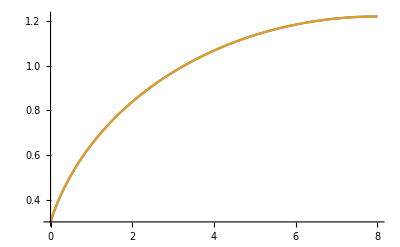

```mathematica
With[{P=0.0327},Plot[{f[x,0.00049]/.sol,1/(80 √(9-√(81+2560000 P)))(√(-576 (-9+√(81+2560000 P))+16 (-1280000 P+9 (-9+√(81+2560000 P))) x+(81+1280000 P-9 √(81+2560000 P)) x^2))},{x,0,8}]]
```

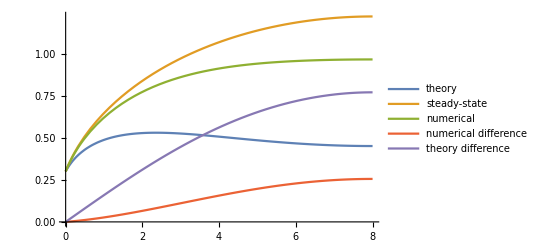

```mathematica
a0=0.06755564087081681;
a1=19.720561339738595;
a2=76.81985966506535;
a3=-4.8012412290665845;
fs2[x_,n_,L_,t_,a0_,a1_,a2_,a3_]:=(2*NIntegrate[((3/10)-a0*Sqrt[a1+a2*x0+a3*x0^2])*Sin[(n-1/2)*Pi*x0/L], {x0,0, L}]/L)*Sin[(2n-1)*Pi*x/(2*L)]Exp[-((2n-1)*Pi/(2*L))^2*kappa*t];
rise = a0*Sqrt[a1+a2*x+a3*x^2];
For[loop0=1,loop0<10,loop0++,rise=rise+fs2[x,loop0,length,0.00005,a0,a1,a2,a3]]
Plot[{rise,a0*Sqrt[a1+a2*x+a3*x^2],f[x,0.00005]/.sol, a0*Sqrt[a1+a2*x+a3*x^2]-f[x,0.00005]/.sol,a0*Sqrt[a1+a2*x+a3*x^2]-rise},{x,0,8},PlotRange->All,PlotLegends->{"theory","steady-state","numerical","numerical difference","theory difference"}]
```

```mathematica
NFourierSeries[-a0*Sqrt[a1+a2*x+a3*x^2]+f[x,0.0001]/.sol,x,16,FourierParameters->{1,Pi/8}]//Chop
```

{(-16339.4-0.611688 ⅈ)+(13688.8+6476.52 ⅈ) ⅇ^(-1/8 ⅈ π x)+(13689.6-6476.16 ⅈ) ⅇ^((ⅈ π x)/8)-(8510.53+8909.14 ⅈ) ⅇ^(-1/4 ⅈ π x)-(8510.8-8909.19 ⅈ) ⅇ^((ⅈ π x)/4)+(4697.45+8162.48 ⅈ) ⅇ^(-3/8 ⅈ π x)+(4697.69-8162.42 ⅈ) ⅇ^((3 ⅈ π x)/8)-(2799.16+6782.93 ⅈ) ⅇ^(-1/2 ⅈ π x)-(2799.31-6782.95 ⅈ) ⅇ^((ⅈ π x)/2)+(1844.42+5683.77 ⅈ) ⅇ^(-5/8 ⅈ π x)+(1844.56-5683.74 ⅈ) ⅇ^((5 ⅈ π x)/8)-(1299.33+4855.18 ⅈ) ⅇ^(-3/4 ⅈ π x)-(1299.43-4855.2 ⅈ) ⅇ^((3 ⅈ π x)/4)+(963.4+4223.83 ⅈ) ⅇ^(-7/8 ⅈ π x)+(963.493-4223.82 ⅈ) ⅇ^((7 ⅈ π x)/8)-(741.743+3731.4 ⅈ) ⅇ^(-ⅈ π x)-(741.824-3731.41 ⅈ) ⅇ^(ⅈ π x)+(588.423+3338.6 ⅈ) ⅇ^(-9/8 ⅈ π x)+(588.494-3338.59 ⅈ) ⅇ^((9 ⅈ π x)/8)-(477.933+3018.8 ⅈ) ⅇ^(-5/4 ⅈ π x)-(477.999-3018.81 ⅈ) ⅇ^((5 ⅈ π x)/4)+(395.816+2753.86 ⅈ) ⅇ^(-11/8 ⅈ π x)+(395.873-2753.85 ⅈ) ⅇ^((11 ⅈ π x)/8)-(333.109+2530.99 ⅈ) ⅇ^(-3/2 ⅈ π x)-(333.165-2531. ⅈ) ⅇ^((3 ⅈ π x)/2)+(284.183+2341.07 ⅈ) ⅇ^(-13/8 ⅈ π x)+(284.23-2341.07 ⅈ) ⅇ^((13 ⅈ π x)/8)-(245.269+2177.37 ⅈ) ⅇ^(-7/4 ⅈ π x)-(245.318-2177.37 ⅈ) ⅇ^((7 ⅈ π x)/4)+(213.824+2034.86 ⅈ) ⅇ^(-15/8 ⅈ π x)+(213.864-2034.86 ⅈ) ⅇ^((15 ⅈ π x)/8)-(188.049+1909.72 ⅈ) ⅇ^(-2 ⅈ π x)-(188.092-1909.72 ⅈ) ⅇ^(2 ⅈ π x)}

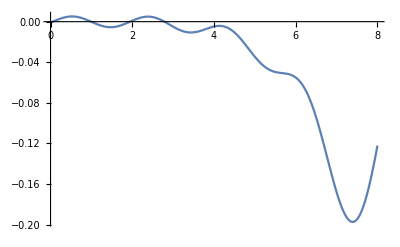

```mathematica
Plot[(-16339.4+27377.6Cos[Pi*x/8]-12953.04Sin[Pi*x/8]-17021.06Cos[2*Pi*x/8]+17818.28Sin[2*Pi*x/8]+9394.9Cos[3*Pi*x/8]-16324.96Sin[3*Pi*x/8]-5598.32Cos[4*Pi*x/8]+13565.9Sin[4*Pi*x/8]+3688.84Cos[5*Pi*x/8]-11367.54Sin[5*Pi*x/8]-2598.66Cos[6*Pi*x/8]+9710.36Sin[6*Pi*x/8]+1926.8Cos[7*Pi*x/8]-8447.66Sin[7*Pi*x/8]-1483.486Cos[8*Pi*x/8]+7462.82Sin[8*Pi*x/8])/700000,{x,0,8}]
```

```mathematica
rise
```

0.0620957 √(19.7206+76.8199 x-4.80124 x^2)-0.535875 Sin[(π x)/16]-0.000959284 Sin[(3 π x)/16]-7.90718×10^-8 Sin[(5 π x)/16]-1.37458×10^-13 Sin[(7 π x)/16]-4.27107×10^-21 Sin[(9 π x)/16]-2.22078×10^-30 Sin[(11 π x)/16]-1.86497×10^-41 Sin[(13 π x)/16]-2.46853×10^-54 Sin[(15 π x)/16]-5.03772×10^-69 Sin[(17 π x)/16]

```mathematica
c[1]/c[0.3]
```

37.037